```mathematica
$Assumptions=And[x>0,M≥2,α>1,s>0,q>0,q<1,M/2∈Integers];
```

```mathematica
Solve[(1-x)(1+x^2) +2x(1+x)Log[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(1-x) (1+x^2)+2 x (1+x) Log[x]==0,x]

```mathematica
x/.FindRoot[(1-x)(1+x^2) +2x(1+x)Log[x]==0,{x,1.1}]
```

1.

```mathematica
x/.FindRoot[(1-x)(1+x^2) +2x(1+x)Log[x]==0,{x,0.1}]
```

0.221899

```mathematica
xs=x/.FindRoot[(1-x)(1+x^2) +2x(1+x)Log[x]==0,{x,5}]
```

4.50656

```mathematica
NumberForm[4.506561365460805,16]
```

4.506561365460805

```mathematica
ABsol=Solve[{((1-q)α^2+(q-2)α+1)A+(α^2+(q-2)α+(1-q))B==0,α^(M/2)A+α^(1-M/2)B==(-2α)/((1+α)s)},{A,B}][[1]]
```

{A→-(2 α^(1+M/2) (-1+q+α))/(s (1+α) (α-α^2+q α^2-α^M+q α^M+α^(1+M))),B→-(2 α^(1+M/2) (1-α+q α))/(s (1+α) (α-α^2+q α^2-α^M+q α^M+α^(1+M)))}

```mathematica
FullSimplify[A/.ABsol]
```

-(2 α^(1+M/2) (-1+q+α))/(s (1+α) (α+(-1+q) α^2+α^M (-1+q+α)))

```mathematica
FullSimplify[B/.ABsol]
```

-(2 α^(1+M/2) (1+(-1+q) α))/(s (1+α) (α+(-1+q) α^2+α^M (-1+q+α)))

```mathematica
FullSimplify[(A+B)/.ABsol]
```

-(2 q α^(1+M/2))/(s α^M (-1+q+α)+s α (1+(-1+q) α))

```mathematica
eta=FullSimplify[(A+B+1/s)/.ABsol]
```

(1-(2 q α^(1+M/2))/(α+(-1+q) α^2+α^M (-1+q+α)))/s

```mathematica
lapl=(2q eta)/(2+(M-2)q)//Expand//FullSimplify
```

(2 q (1-(2 q α^(1+M/2))/(α+(-1+q) α^2+α^M (-1+q+α))))/((2+(-2+M) q) s)

```mathematica
qder=D[lapl,q]//Expand//FullSimplify
```

(4 (q (q (2+M (-1+α)-4 α)+4 (-1+α)) α^(2+M/2)-q (q (4+M (-1+α)-2 α)+4 (-1+α)) α^(1+(3 M)/2)+α^(2 M) (-1+q+α)^2+2 α^(1+M) (-1+q+α) (1+(-1+q) α)+(α+(-1+q) α^2)^2))/((2+(-2+M) q)^2 s (α+(-1+q) α^2+α^M (-1+q+α))^2)

```mathematica
qsol=Solve[q (q (2+M (-1+α)-4 α)+4 (-1+α)) α^(2+M/2)-q (q (4+M (-1+α)-2 α)+4 (-1+α)) α^(1+(3 M)/2)+α^(2 M) (-1+q+α)^2+2 α^(1+M) (-1+q+α) (1+(-1+q) α)+(α+(-1+q) α^2)^2==0,q]
```

{{q→(-2 α^3+2 α^4+4 α^(2+M/2)-4 α^(3+M/2)+2 α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(3+M)-4 α^(1+(3 M)/2)+4 α^(2+(3 M)/2)-2 α^(1+2 M)-√((2 α^3-2 α^4-4 α^(2+M/2)+4 α^(3+M/2)-2 α^(2 M)+2 α^(1+M)-4 α^(2+M)+2 α^(3+M)+4 α^(1+(3 M)/2)-4 α^(2+(3 M)/2)+2 α^(1+2 M))^2-4 (α^4+2 α^(2+M/2)-M α^(2+M/2)-4 α^(3+M/2)+M α^(3+M/2)+α^(2 M)+2 α^(2+M)-4 α^(1+(3 M)/2)+M α^(1+(3 M)/2)+2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)) (α^2-2 α^3+α^4+α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(3+M)-2 α^(1+2 M)+α^(2+2 M))))/(2 (α^4+2 α^(2+M/2)-M α^(2+M/2)-4 α^(3+M/2)+M α^(3+M/2)+α^(2 M)+2 α^(2+M)-4 α^(1+(3 M)/2)+M α^(1+(3 M)/2)+2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)))},{q→(-2 α^3+2 α^4+4 α^(2+M/2)-4 α^(3+M/2)+2 α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(3+M)-4 α^(1+(3 M)/2)+4 α^(2+(3 M)/2)-2 α^(1+2 M)+√((2 α^3-2 α^4-4 α^(2+M/2)+4 α^(3+M/2)-2 α^(2 M)+2 α^(1+M)-4 α^(2+M)+2 α^(3+M)+4 α^(1+(3 M)/2)-4 α^(2+(3 M)/2)+2 α^(1+2 M))^2-4 (α^4+2 α^(2+M/2)-M α^(2+M/2)-4 α^(3+M/2)+M α^(3+M/2)+α^(2 M)+2 α^(2+M)-4 α^(1+(3 M)/2)+M α^(1+(3 M)/2)+2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)) (α^2-2 α^3+α^4+α^(2 M)-2 α^(1+M)+4 α^(2+M)-2 α^(3+M)-2 α^(1+2 M)+α^(2+2 M))))/(2 (α^4+2 α^(2+M/2)-M α^(2+M/2)-4 α^(3+M/2)+M α^(3+M/2)+α^(2 M)+2 α^(2+M)-4 α^(1+(3 M)/2)+M α^(1+(3 M)/2)+2 α^(2+(3 M)/2)-M α^(2+(3 M)/2)))}}

```mathematica
Dimensions[qsol]
```

{2,1}

```mathematica
q1=FullSimplify[q/.qsol[[2]],α^M>α]
```

((-1+α) (α-α^M) (α^2-2 α^(1+M/2)+α^M-α^((2+M)/4) √(4 α^(1+M/2)+(M (-1+α)-2 α) α^M+α (-2+M-M α))))/(α^4+(2+M (-1+α)-4 α) α^(2+M/2)+α^(2 M)+2 α^(2+M)+α^(1+(3 M)/2) (-4+M+2 α-M α))

```mathematica
q2=FullSimplify[q/.qsol[[1]],α^M>α]
```

((-1+α) (α-α^M) (α^2-2 α^(1+M/2)+α^M+α^((2+M)/4) √(4 α^(1+M/2)+(M (-1+α)-2 α) α^M+α (-2+M-M α))))/(α^4+(2+M (-1+α)-4 α) α^(2+M/2)+α^(2 M)+2 α^(2+M)+α^(1+(3 M)/2) (-4+M+2 α-M α))

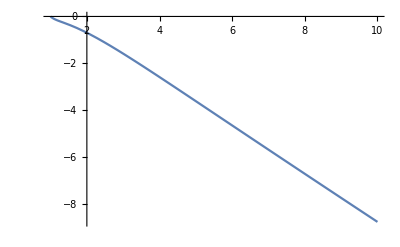

```mathematica
Plot[q1/.M->12,{α,1,10}]
```

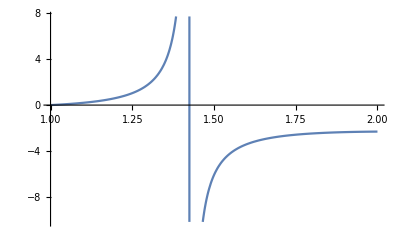

```mathematica
Plot[q2/.M->12,{α,1,2}]
```

```mathematica
Limit[q2,α->1]
```

0

```mathematica
xs^(1/6)
```

1.28521

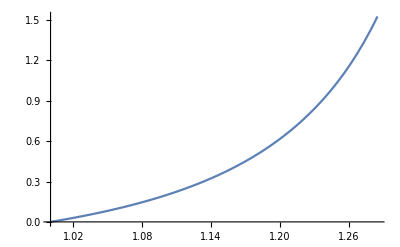

```mathematica
Plot[q2/.M->12,{α,1,xs^(1/6)}]
```

```mathematica
q2/.{M->12,α->xs^(1/6)}
```

1.52706

```mathematica
qn=Numerator[q2]/((-1+α) (α-α^M))
```

α^2-2 α^(1+M/2)+α^M+α^(1/2+M/4) √(4 α^(1+M/2)+(M (-1+α)-2 α) α^M+α (-2+M-M α))

```mathematica
qd=Denominator[q2]/((-1+α) (α-α^M))
```

(α^4+(2+M (-1+α)-4 α) α^(2+M/2)+α^(2 M)+2 α^(2+M)+α^(1+(3 M)/2) (-4+M+2 α-M α))/((-1+α) (α-α^M))

```mathematica
FullSimplify[(-1+α)^2 (α-α^M)^2((qn-(α^2-2 α^(1+M/2)+α^M))^2-(qd-(α^2-2 α^(1+M/2)+α^M))^2)//Expand]
```

-α (α^4+(2+M (-1+α)-4 α) α^(2+M/2)+α^(2 M)+2 α^(2+M)+α^(1+(3 M)/2) (-4+M+2 α-M α)) (α+(-2+M (-1+α)) α^(1+M/2)+2 α^(1+M)+α^(1+2 M)+α^(3 M/2) (M-(2+M) α))

```mathematica
aeq1=(α^4+(2+M (-1+α)-4 α) α^(2+M/2)+α^(2 M)+2 α^(2+M)+α^(1+(3 M)/2) (-4+M+2 α-M α))/α^4//Expand
```

1+2 α^(-2+M/2)-M α^(-2+M/2)-4 α^(-1+M/2)+M α^(-1+M/2)+2 α^(-2+M)-4 α^(-3+(3 M)/2)+M α^(-3+(3 M)/2)+2 α^(-2+(3 M)/2)-M α^(-2+(3 M)/2)+α^(-4+2 M)

```mathematica
aeq2=(α+(-2+M (-1+α)) α^(1+M/2)+2 α^(1+M)+α^(1+2 M)+α^(3 M/2) (M-(2+M) α))/α//Expand
```

1+M α^(1+M/2)-2 α^(M/2)-M α^(M/2)+2 α^M-2 α^(3 M/2)-M α^(3 M/2)+α^(2 M)+M α^(-1+(3 M)/2)

```mathematica
PolynomialQuotient[aeq2,1-α,α]
```

PolynomialQuotient[1+M α^(1+M/2)-2 α^(M/2)-M α^(M/2)+2 α^M-2 α^(3 M/2)-M α^(3 M/2)+α^(2 M)+M α^(-1+(3 M)/2),1-α,α]

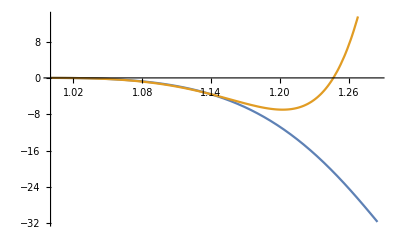

```mathematica
Plot[{aeq1/.{M->12},aeq2/.{M->12}},{α,1,xs^(1/6)}]
```

```mathematica
FullSimplify[qder/.q->1]
```

(4 (α+(-2+M (-1+α)) α^(1+M/2)+2 α^(1+M)+α^(1+2 M)+α^(3 M/2) (M-(2+M) α)))/(M^2 s α (1+α^M)^2)

```mathematica
as[MM_]:=α/.FindRoot[(aeq2/.M->MM)==0,{α,xs^(2/MM)}][[1]]
```

```mathematica
as[12]
```

1.24673

```mathematica
tau[MM_]:=(2as[MM])/(as[MM]-1)^2
```

```mathematica
SetAttributes[tau,NumericFunction]
```

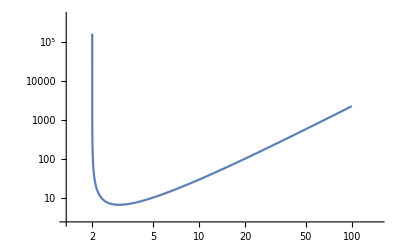

```mathematica
LogLogPlot[tau[m],{m,2,100}]
```

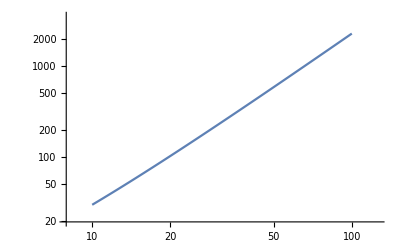

```mathematica
LogLogPlot[tau[m],{m,10,100}]
```

```mathematica
mtable=Table[m,{m,10,100}];
```

```mathematica
tautable=Table[tau[m],{m,10,101}];
```

```mathematica
tautable2=Table[tau[m],{m,10,100}];
```

```mathematica
difftautable=Differences[tautable];
```

```mathematica
logdifftau=mtable*difftautable/tautable2;
```

```mathematica
logdifftau[[91]]
```

1.97881

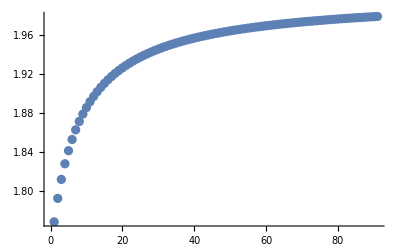

```mathematica
ListPlot[logdifftau]
```

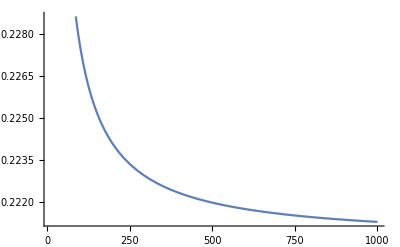

```mathematica
Plot[tau[m]/m^2,{m,10,1000}]
```

```mathematica
1/(2 Log[xs]^2)
```

0.220591

```mathematica
2 Log[xs]^2
```

4.53327

```mathematica
FullSimplify[ aeq1/.M->12]
```

1+α^4 (-10+α (8+α^5 (2+α^5 (8-10 α+α^5))))

```mathematica
FullSimplify[ aeq1/.M->2]
```

0

```mathematica
FullSimplify[ aeq2/.M->2]
```

(-1+α)^4

```mathematica
FullSimplify[ aeq2/.M->12]
```

1+α^6 (-14+α (12+α^5 (2+α^5 (12-14 α+α^7))))

```mathematica
lapl/.{q->0}
```

0

```mathematica
Limit[lapl/.{s->(α-1)^2/(2α)},α->1]
```

(-4+4 M+4 q-4 M q+M^2 q)/(4+2 (-2+M) q)

```mathematica
FullSimplify[lapl/.{q->1}]
```

(2 (-1+α^(M/2))^2)/(M s (1+α^M))

```mathematica
<<ToMatlab`
```

```mathematica
PrintMatlab[lapl/.{α->alpha,M->numstates}]
```

2.*q.*(2+((-2)+numstates).*q).^(-1).*(1+(-2).*alpha.^(1+( ...
  1/2).*numstates).*q.*(alpha+alpha.^2.*((-1)+q)+ ...
  alpha.^numstates.*((-1)+alpha+q)).^(-1)).*s.^(-1);

```mathematica
PrintMatlab[q2/.{α->alpha,M->numstates}]
```

((-1)+alpha).*(alpha+(-1).*alpha.^numstates).*(alpha.^4+ ...
  alpha.^(2.*numstates)+2.*alpha.^(2+numstates)+alpha.^(2+( ...
  1/2).*numstates).*(2+(-4).*alpha+((-1)+alpha).*numstates)+ ...
  alpha.^(1+(3/2).*numstates).*((-4)+2.*alpha+numstates+(-1).* ...
  alpha.*numstates)).^(-1).*(alpha.^2+(-2).*alpha.^(1+(1/2).* ...
  numstates)+alpha.^numstates+alpha.^((1/4).*(2+numstates)).*( ...
  4.*alpha.^(1+(1/2).*numstates)+alpha.^numstates.*((-2).* ...
  alpha+((-1)+alpha).*numstates)+alpha.*((-2)+numstates+(-1).* ...
  alpha.*numstates)).^(1/2));

```mathematica
PrintMatlab[aeq2/.{α->alpha,M->numstates}]
```

1+(-2).*alpha.^((1/2).*numstates)+2.*alpha.^numstates+(-2).* ...
  alpha.^((3/2).*numstates)+alpha.^(2.*numstates)+alpha.^(1+( ...
  1/2).*numstates).*numstates+(-1).*alpha.^((1/2).*numstates) ...
  .*numstates+(-1).*alpha.^((3/2).*numstates).*numstates+ ...
  alpha.^((-1)+(3/2).*numstates).*numstates;

```mathematica
Limit[q2,M->∞,Assumptions->α>1]
```

1-α

```mathematica
FullSimplify[lapl/.{q->1-α}]
```

(2 (-1+α) (1+α-2 α^(M/2)))/(s (M (-1+α)-2 α) (1+α))

```mathematica
Series[FullSimplify[FullSimplify[lapl/.{q->1-α}]/.{α->s+1+√(s(s+2))}],{s,0,1}]//Simplify
```

(-1+M)+((2-6 M+3 M^2) √s)/(2 √2)+5/6 M (2-3 M+M^2) s+O[s]^(3/2)